```mathematica
a={3,3,-4,1};
b={5,3,-4,1};
c={5,5,-4,1};
d={3,5,-4,1};
aPrime={3,3,-6,1};
bPrime={5,3,-6,1};
cPrime={5,5,-6,1};
dPrime={3,5,-6,1};
d2Prime={8,8,-6,1};
Oc={0,0,0,1};
Oc2={6,0,3,1};
zeta1 = -2;
zeta2=-1;
alpha=45;
beta = 0;
Oc2={6,0,3,1};
Rot1=RotationsE2[alpha];
Rot2=RotationsE2[beta];
ObjectSize = b[[1]]-a[[1]];
```

```mathematica
ClearAll["Global`*"];
```

OC2 = {6,0,3,1}

M of C2=(1/(√2) | 0 | -1/(√2) | -3/(√2)
0 | 1 | 0 | 0
1/(√2) | 0 | 1/(√2) | -9/(√2)
0 | 0 | 0 | 1)

M2 of C1 =(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

ProjectionMtxCamera1(-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 1 | 0)

ProjectionMtxCamera2(-1/(√2) | 0 | 1/(√2) | -3/(√2)+3 √2
0 | -1 | 0 | 0
-1/(√2) | 0 | -1/(√2) | 3/(√2)+3 √2
1/(√2) | 0 | 1/(√2) | -3/(√2)-3 √2)

CameraProjectedPointsK1 = (-6 | -6 | 8 | -4
-10 | -6 | 8 | -4
-10 | -10 | 8 | -4
-6 | -10 | 8 | -4
-6 | -6 | 12 | -6
-10 | -6 | 12 | -6
-10 | -10 | 12 | -6
-6 | -10 | 12 | -6
-16 | -16 | 12 | -6)

CameraProjectedPointsK2 = (-2 √2 | -3 | 5 √2 | -5 √2
-3 √2 | -3 | 4 √2 | -4 √2
-3 √2 | -5 | 4 √2 | -4 √2
-2 √2 | -5 | 5 √2 | -5 √2
-3 √2 | -3 | 6 √2 | -6 √2
-4 √2 | -3 | 5 √2 | -5 √2
-4 √2 | -5 | 5 √2 | -5 √2
-3 √2 | -5 | 6 √2 | -6 √2
-11/(√2) | -8 | 7/(√2) | -7/(√2))

homogene CameraProjectedPointsK1 = (3/2 | 3/2 | -2 | 1
5/2 | 3/2 | -2 | 1
5/2 | 5/2 | -2 | 1
3/2 | 5/2 | -2 | 1
1 | 1 | -2 | 1
5/3 | 1 | -2 | 1
5/3 | 5/3 | -2 | 1
1 | 5/3 | -2 | 1
8/3 | 8/3 | -2 | 1)

homogene CameraProjectedPointsK2 = (2/5 | 3/(5 √2) | -1 | 1
3/4 | 3/(4 √2) | -1 | 1
3/4 | 5/(4 √2) | -1 | 1
2/5 | 1/(√2) | -1 | 1
1/2 | 1/(2 √2) | -1 | 1
4/5 | 3/(5 √2) | -1 | 1
4/5 | 1/(√2) | -1 | 1
1/2 | 5/(6 √2) | -1 | 1
11/7 | (8 √2)/7 | -1 | 1)

Begin construct Epipol_______________________________________________

End construct Epipol_______________________________________________

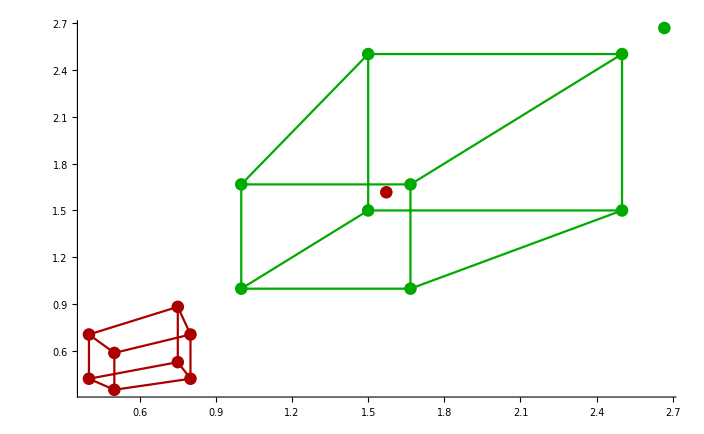

ImagePlaneC1Points = (3/2 | 3/2 | 1
5/2 | 3/2 | 1
5/2 | 5/2 | 1
3/2 | 5/2 | 1
1 | 1 | 1
5/3 | 1 | 1
5/3 | 5/3 | 1
1 | 5/3 | 1
8/3 | 8/3 | 1)

ImagePlaneC2Points = (2/5 | 3/(5 √2) | 1
3/4 | 3/(4 √2) | 1
3/4 | 5/(4 √2) | 1
2/5 | 1/(√2) | 1
1/2 | 1/(2 √2) | 1
4/5 | 3/(5 √2) | 1
4/5 | 1/(√2) | 1
1/2 | 5/(6 √2) | 1
11/7 | (8 √2)/7 | 1)

CoefficientMtx = (3/5 | 3/5 | 2/5 | 9/(10 √2) | 9/(10 √2) | 3/(5 √2) | 3/2 | 3/2 | 1
15/8 | 9/8 | 3/4 | 15/(8 √2) | 9/(8 √2) | 3/(4 √2) | 5/2 | 3/2 | 1
15/8 | 15/8 | 3/4 | 25/(8 √2) | 25/(8 √2) | 5/(4 √2) | 5/2 | 5/2 | 1
3/5 | 1 | 2/5 | 3/(2 √2) | 5/(2 √2) | 1/(√2) | 3/2 | 5/2 | 1
1/2 | 1/2 | 1/2 | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1 | 1 | 1
4/3 | 4/5 | 4/5 | 1/(√2) | 3/(5 √2) | 3/(5 √2) | 5/3 | 1 | 1
4/3 | 4/3 | 4/5 | 5/(3 √2) | 5/(3 √2) | 1/(√2) | 5/3 | 5/3 | 1
1/2 | 5/6 | 1/2 | 5/(6 √2) | 25/(18 √2) | 5/(6 √2) | 1 | 5/3 | 1
88/21 | 88/21 | 11/7 | (64 √2)/21 | (64 √2)/21 | (8 √2)/7 | 8/3 | 8/3 | 1)

RowReduce CoefficientMtx = [(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | -3 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | √2 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 4 √2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)]

ns ={{0,3,0,-√2,0,-4 √2,0,1,0}}

F = (0. | 3. | 0.
-1.41421 | 0. | -5.65685
0. | 1. | 0.)

lC1 = {{4.5,-7.77817,1.5},{4.5,-9.19239,1.5},{7.5,-9.19239,2.5},{7.5,-7.77817,2.5},{3.,-7.07107,1.},{3.,-8.01388,1.},{5.,-8.01388,1.66667},{5.,-7.07107,1.66667},{8.,-9.42809,2.66667}}

lPrimeC1 = {{-0.6,2.2,-2.4},{-0.75,3.25,-3.},{-1.25,3.25,-5.},{-1.,2.2,-4.},{-0.5,2.5,-2.},{-0.6,3.4,-2.4},{-1.,3.4,-4.},{-0.833333,2.5,-3.33333},{-2.28571,5.71429,-9.14286}}

e = {-4,0,1}

e' = {-1/3,0,1}

EpipoleLines = (3 | -(11 √2)/3 | 1
3 | -(13 √2)/3 | 1
3 | -(13 √2)/5 | 1
3 | -(11 √2)/5 | 1
3 | -5 √2 | 1
3 | -(17 √2)/3 | 1
3 | -(17 √2)/5 | 1
3 | -3 √2 | 1
3 | -5/(√2) | 1)

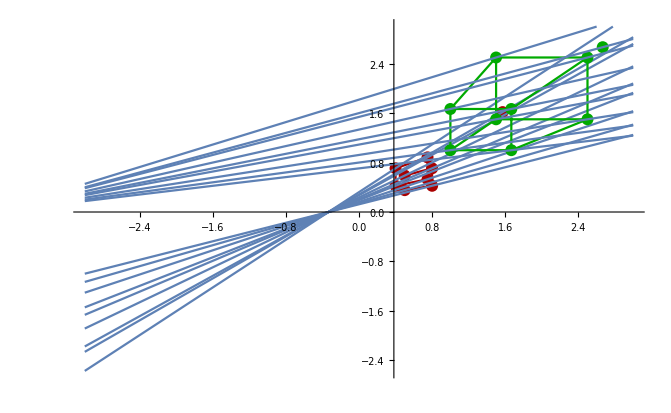

Start Rectification_________________________________________________________________________

z = {0,1,0}

wPrime = {-1,0,-1/3}

w = {-1,0,-4}

wPrime = {3,0,1}

w = {1/4,0,1}

HpPrime = (1 | 0 | 0
0 | 1 | 0
3 | 0 | 1)

Hp = (1 | 0 | 0
0 | 1 | 0
1/4 | 0 | 1)

ePrime inf = {-1/3,0,0}

e inf = {-4,0,0}

HrPrime = (4 √2 | 0 | 0
0 | 4 √2 | 0
0 | 0 | 1)

Hr = (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

ePrimeHorizontal = {-(4 √2)/3,0,0}

eHorizontal = {-4,0,0}

RecPointsC2 =((8 √2)/11 | 12/11 | 1
(12 √2)/13 | 12/13 | 1
(12 √2)/13 | 20/13 | 1
(8 √2)/11 | 20/11 | 1
(4 √2)/5 | 4/5 | 1
(16 √2)/17 | 12/17 | 1
(16 √2)/17 | 20/17 | 1
(4 √2)/5 | 4/3 | 1)

RecPointsC1 =(12/11 | 12/11 | 1
20/13 | 12/13 | 1
20/13 | 20/13 | 1
12/11 | 20/11 | 1
4/5 | 4/5 | 1
20/17 | 12/17 | 1
20/17 | 20/17 | 1
4/5 | 4/3 | 1)

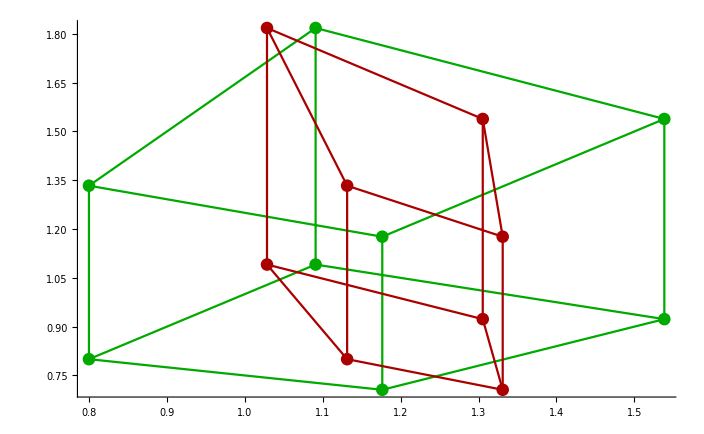

End Rectification___________________________________________________________________________

Begin Computing essential Matrix___________________________________________________

EMtx = {{0,3/(2 √2),0},{-1/2,0,1},{0,-1/(2 √2),0}}

U of E = {{0,3/(√10),1/(√10)},{1,0,0},{0,-1/(√10),3/(√10)}}

Sigma of E = {{(√5)/2,0,0},{0,(√5)/2,0},{0,0,0}}

V of E = {{-1/(√5),0,2/(√5)},{0,1,0},{2/(√5),0,1/(√5)}}

S1 = (0 | 3/(√10) | 0
-3/(√10) | 0 | 1/(√10)
0 | -1/(√10) | 0)

S2 = (0 | -3/(√10) | 0
3/(√10) | 0 | -1/(√10)
0 | 1/(√10) | 0)

R1 = (3/(5 √2)+(√2)/5 | 0 | 1/(5 √2)-(3 √2)/5
0 | 1 | 0
-1/(5 √2)+(3 √2)/5 | 0 | 3/(5 √2)+(√2)/5)

R2 = (-3/(5 √2)+(√2)/5 | 0 | 1/(5 √2)+(3 √2)/5
0 | -1 | 0
1/(5 √2)+(3 √2)/5 | 0 | 3/(5 √2)-(√2)/5)

{{3/(5 √2)+(√2)/5,0,1/(5 √2)-(3 √2)/5},{0,1,0},{-1/(5 √2)+(3 √2)/5,0,3/(5 √2)+(√2)/5}} is no Rotation

{{-3/(5 √2)+(√2)/5,0,1/(5 √2)+(3 √2)/5},{0,-1,0},{1/(5 √2)+(3 √2)/5,0,3/(5 √2)-(√2)/5}} is no Rotation

Check if t of S1, S2 is equal = {{{1/3,0,1}},{{1/3,0,1}}}

t = {1/3,0,1}

P21  = (-3/(5 √2)+(√2)/5 | 0 | 1/(5 √2)+(3 √2)/5 | -1/3
0 | -1 | 0 | 0
1/(5 √2)+(3 √2)/5 | 0 | 3/(5 √2)-(√2)/5 | -1)

P22  = (3/(5 √2)+(√2)/5 | 0 | 1/(5 √2)-(3 √2)/5 | -1/3
0 | 1 | 0 | 0
-1/(5 √2)+(3 √2)/5 | 0 | 3/(5 √2)+(√2)/5 | -1)

P23  = (-3/(5 √2)+(√2)/5 | 0 | 1/(5 √2)+(3 √2)/5 | 1/3
0 | -1 | 0 | 0
1/(5 √2)+(3 √2)/5 | 0 | 3/(5 √2)-(√2)/5 | 1)

P24  = (3/(5 √2)+(√2)/5 | 0 | 1/(5 √2)-(3 √2)/5 | 1/3
0 | 1 | 0 | 0
-1/(5 √2)+(3 √2)/5 | 0 | 3/(5 √2)+(√2)/5 | 1)

End Computing essential Matrix___________________________________________________

Triangulation: WorldPoint reconstruction ___________________________________________________

C2Oc2 = {-1/3,0,-1}

-Rot1 = (-1/(√2) | 0 | -1/(√2)
0 | -1 | 0
1/(√2) | 0 | -1/(√2))

WOc2 = {(2 √2)/3,0,(√2)/3}

ImagePlaneC1PointsWorld =(3/2 | 3/2 | -2 | 1
5/2 | 3/2 | -2 | 1
5/2 | 5/2 | -2 | 1
3/2 | 5/2 | -2 | 1
1 | 1 | -2 | 1
5/3 | 1 | -2 | 1
5/3 | 5/3 | -2 | 1
1 | 5/3 | -2 | 1
8/3 | 8/3 | -2 | 1)

ImagePlaneC2PointsWorld =(11/(15 √2) | 3/(5 √2) | -11/(15 √2) | 1
13/(12 √2) | 3/(4 √2) | -13/(12 √2) | 1
13/(12 √2) | 5/(4 √2) | -13/(12 √2) | 1
11/(15 √2) | 1/(√2) | -11/(15 √2) | 1
5/(6 √2) | 1/(2 √2) | -5/(6 √2) | 1
17/(15 √2) | 3/(5 √2) | -17/(15 √2) | 1
17/(15 √2) | 1/(√2) | -17/(15 √2) | 1
5/(6 √2) | 5/(6 √2) | -5/(6 √2) | 1
(20 √2)/21 | (8 √2)/7 | -(20 √2)/21 | 1)

LinesC1 = {{3/2+(3 t)/2,3/2+(3 t)/2,-2-2 t},{5/2+(5 t)/2,3/2+(3 t)/2,-2-2 t},{5/2+(5 t)/2,5/2+(5 t)/2,-2-2 t},{3/2+(3 t)/2,5/2+(5 t)/2,-2-2 t},{1+t,1+t,-2-2 t},{5/3+(5 t)/3,1+t,-2-2 t},{5/3+(5 t)/3,5/3+(5 t)/3,-2-2 t},{1+t,5/3+(5 t)/3,-2-2 t},{8/3+(8 t)/3,8/3+(8 t)/3,-2-2 t}}

LinesC2 = {{(11-9 t2)/(15 √2),(3 (1+t2))/(5 √2),-(11+21 t2)/(15 √2)},{(13-3 t2)/(12 √2),(3 (1+t2))/(4 √2),-(13+21 t2)/(12 √2)},{(13-3 t2)/(12 √2),(5 (1+t2))/(4 √2),-(13+21 t2)/(12 √2)},{(11-9 t2)/(15 √2),(1+t2)/(√2),-(11+21 t2)/(15 √2)},{(5-3 t2)/(6 √2),(1+t2)/(2 √2),-(5+9 t2)/(6 √2)},{(17-3 t2)/(15 √2),(3 (1+t2))/(5 √2),-(17+27 t2)/(15 √2)},{(17-3 t2)/(15 √2),(1+t2)/(√2),-(17+27 t2)/(15 √2)},{(5-3 t2)/(6 √2),(5 (1+t2))/(6 √2),-(5+9 t2)/(6 √2)},{2/21 √2 (10+3 t2),8/7 √2 (1+t2),-1/21 √2 (20+27 t2)}}

t & t2 = {t→-1+(2 √2)/9,t2→1/9,t→-1+(2 √2)/9,t2→-1/9,t→-1+(2 √2)/9,t2→-1/9,t→-1+(2 √2)/9,t2→1/9,t→1/3 (-3+√2),t2→1/3,t→1/3 (-3+√2),t2→1/9,t→1/3 (-3+√2),t2→1/9,t→1/3 (-3+√2),t2→1/3,t→1/3 (-3+√2),t2→-2/9}

ReconstructedPointsC1 = {{{{0.471405},{0.471405},{-0.628539}}},{{{0.785674},{0.471405},{-0.628539}}},{{{0.785674},{0.785674},{-0.628539}}},{{{0.471405},{0.785674},{-0.628539}}},{{{0.471405},{0.471405},{-0.942809}}},{{{0.785674},{0.471405},{-0.942809}}},{{{0.785674},{0.785674},{-0.942809}}},{{{0.471405},{0.785674},{-0.942809}}}}

ReconstructedPointsC2 = {{{{0.471405},{0.471405},{-0.628539}}},{{{0.785674},{0.471405},{-0.628539}}},{{{0.785674},{0.785674},{-0.628539}}},{{{0.471405},{0.785674},{-0.628539}}},{{{0.471405},{0.471405},{-0.942809}}},{{{0.785674},{0.471405},{-0.942809}}},{{{0.785674},{0.785674},{-0.942809}}},{{{0.471405},{0.785674},{-0.942809}}}}

scaleValueC1 = {6.36396}

ResizedPointsC1 = {{{{3.},{3.},{-4.}}},{{{5.},{3.},{-4.}}},{{{5.},{5.},{-4.}}},{{{3.},{5.},{-4.}}},{{{3.},{3.},{-6.}}},{{{5.},{3.},{-6.}}},{{{5.},{5.},{-6.}}},{{{3.},{5.},{-6.}}}}

scaleValueC2 = {6.36396}

ResizedPointsC2 = {{{{3.},{3.},{-4.}}},{{{5.},{3.},{-4.}}},{{{5.},{5.},{-4.}}},{{{3.},{5.},{-4.}}},{{{3.},{3.},{-6.}}},{{{5.},{3.},{-6.}}},{{{5.},{5.},{-6.}}},{{{3.},{5.},{-6.}}}}

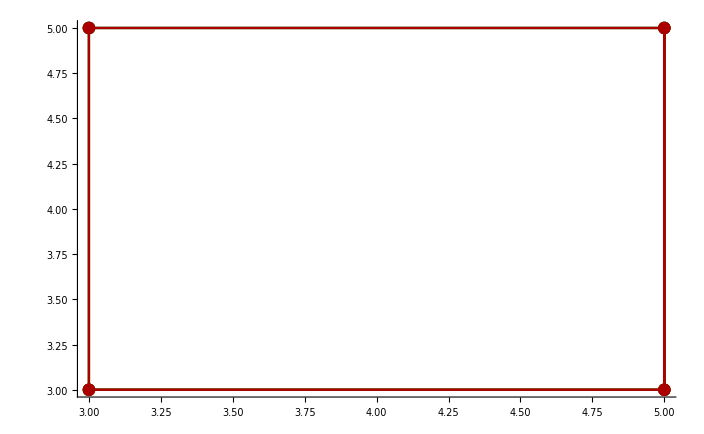

```mathematica
StartComputation[];
```